## Rabi

```mathematica
path="/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/parameter_scans_20190221";
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{path,"rabi_constantfun_scan"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{57,201,3}

{11400,3}

```mathematica
ListPlot3D[joinedDataSets,InterpolationOrder->3,AxesLabel->{"time","height","fidelity"}]
```

-Graphics3D-

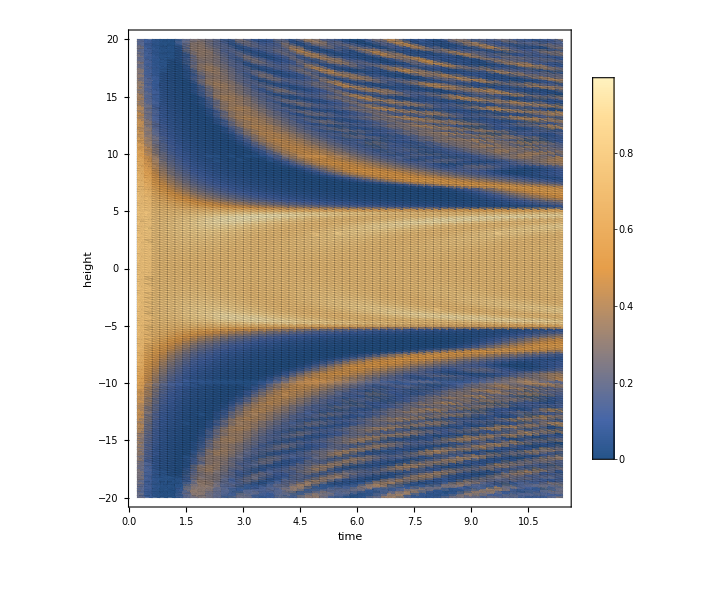

```mathematica
ListDensityPlot[joinedDataSets,PlotLegends->Automatic,Mesh->All,MeshStyle->Directive[Opacity@0.1],FrameLabel->{"time","height"},ImageSize->600]
```

## Rabi finer search

```mathematica
path="/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/parameter_scans_20190221";
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{path,"rabi_constantfun_scan_finerSearch"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{68,201,3}

{13600,3}

```mathematica
ListPlot3D[joinedDataSets,InterpolationOrder->3,AxesLabel->{"time","height","fidelity"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ListDensityPlot[joinedDataSets,PlotLegends->Automatic,Mesh->All,MeshStyle->Directive[Opacity@0.1],FrameLabel->{"time","height"},ImageSize->600]
```

-Graphics-

## LMG

```mathematica
path="/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/parameter_scans_20190221";
dataSets=Import[#,"CSV"]⟦All,2;;⟧&/@(FileNames[FileNameJoin@{FileNameJoin@{path,"lmg_constantfun_scan"},"*"}]);
Dimensions@dataSets

joinedDataSets=Join@@(Rest/@dataSets);
Dimensions@joinedDataSets
```

{80,201,3}

{16000,3}

```mathematica
ListDensityPlot[joinedDataSets,
PlotLegends->Automatic,Mesh->All,MeshStyle->Directive[Opacity@0.1],FrameLabel->{"time","height"},ImageSize->600
]
```

-Graphics-

```mathematica
ListPlot3D[joinedDataSets,
AxesLabel->{"time","height","fidelity"},PlotRange->{All,All,All},InterpolationOrder->1,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,ImageSize->600
]
```

-Graphics3D-

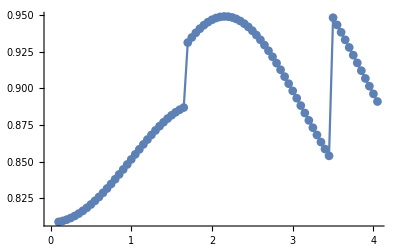

```mathematica
bestFidelityPerTime=Function[dataset,
First@dataset⟦Ordering[#,-1,#1⟦3⟧<#2⟦3⟧&]&[dataset⟦2;;,All⟧]⟧
]/@dataSets;
ListPlot[bestFidelityPerTime⟦All,{1,3}⟧,Joined->True,PlotMarkers->Automatic]
```

```mathematica
bestFidelityPerTime⟦All,{1,2,3}⟧//TableForm
```

0.1 | 0.301508 | 0.809032
0.15 | 0.301508 | 0.809674
0.2 | 0.301508 | 0.810568
0.25 | 0.301508 | 0.81171
0.3 | 0.301508 | 0.813094
0.35 | 0.301508 | 0.814714
0.4 | 0.301508 | 0.816561
0.45 | 0.301508 | 0.818626
0.5 | 0.301508 | 0.820899
0.55 | 0.301508 | 0.823366
0.6 | 0.301508 | 0.826015
0.65 | 0.301508 | 0.82883
0.7 | 0.301508 | 0.831796
0.75 | 0.301508 | 0.834893
0.8 | 0.301508 | 0.838103
0.85 | 0.301508 | 0.841406
0.9 | 0.301508 | 0.844779
0.95 | 0.301508 | 0.848201
1. | 0.301508 | 0.851646
1.05 | 0.301508 | 0.85509
1.1 | 0.301508 | 0.858507
1.15 | 0.301508 | 0.861872
1.2 | 0.301508 | 0.865157
1.25 | 0.301508 | 0.868337
1.3 | 0.301508 | 0.871385
1.35 | 0.301508 | 0.874275
1.4 | 0.301508 | 0.876982
1.45 | 0.301508 | 0.879483
1.5 | 0.301508 | 0.881754
1.55 | 0.301508 | 0.883777
1.6 | 0.301508 | 0.88553
1.65 | 0.301508 | 0.886999
1.7 | 0.502513 | 0.9313
1.75 | 0.502513 | 0.934797
1.8 | 0.502513 | 0.937962
1.85 | 0.502513 | 0.94077
1.9 | 0.502513 | 0.943198
1.95 | 0.502513 | 0.94523
2. | 0.502513 | 0.946848
2.05 | 0.502513 | 0.94804
2.1 | 0.502513 | 0.948798
2.15 | 0.502513 | 0.949117
2.2 | 0.502513 | 0.948996
2.25 | 0.502513 | 0.948436
2.3 | 0.502513 | 0.947444
2.35 | 0.502513 | 0.946029
2.4 | 0.502513 | 0.944205
2.45 | 0.502513 | 0.941987
2.5 | 0.502513 | 0.939393
2.55 | 0.502513 | 0.936446
2.6 | 0.502513 | 0.933168
2.65 | 0.502513 | 0.929586
2.7 | 0.502513 | 0.925726
2.75 | 0.502513 | 0.921616
2.8 | 0.502513 | 0.917286
2.85 | 0.502513 | 0.912765
2.9 | 0.502513 | 0.908083
2.95 | 0.502513 | 0.90327
3. | 0.502513 | 0.898355
3.05 | 0.502513 | 0.893369
3.1 | 0.502513 | 0.888339
3.15 | 0.502513 | 0.883292
3.2 | 0.502513 | 0.878257
3.25 | 0.502513 | 0.873257
3.3 | 0.502513 | 0.868317
3.35 | 0.502513 | 0.863461
3.4 | 0.502513 | 0.858709
3.45 | 0.502513 | 0.854084
3.5 | 0.703518 | 0.948255
3.55 | 0.703518 | 0.943334
3.6 | 0.703518 | 0.938301
3.65 | 0.703518 | 0.933177
3.7 | 0.703518 | 0.92798
3.75 | 0.703518 | 0.922731
3.8 | 0.703518 | 0.917448
3.85 | 0.703518 | 0.912149
3.9 | 0.703518 | 0.906851
3.95 | 0.703518 | 0.901571
4. | 0.703518 | 0.896324
4.05 | 0.703518 | 0.891126